```mathematica
Needs["VariationalMethods`"]
```

```mathematica
Block[
{f,m,μ,β,γ},
m=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m z^3+1-β^2 z^2/2;
EulerEquations[q μ(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-z[t] Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4])-1/z[t]Sqrt[ f[z[t]]-z'[t]^2/f[z[t]]],z[t],t]
]
```

Simplify::time: Time spent on a transformation exceeded 300. seconds, and the transformation was aborted. Increasing the value of TimeConstraint option may improve the result of simplification.

-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0

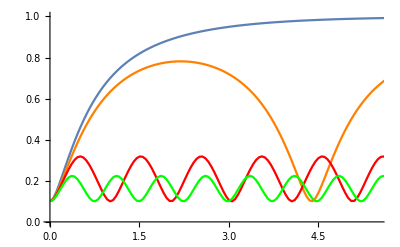

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,0,0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,1.02qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fz1[i,2qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}],PlotStyle->Green],PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

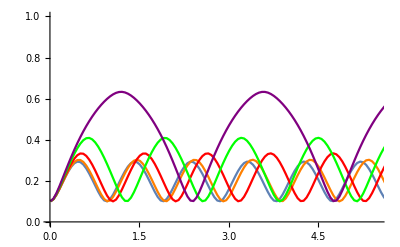

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,0.01,2,0.75μextreme[0.01,2]],0.1,0.01,2,0.75μextreme[0.01,2]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,0.6124,2,0.75μextreme[0.6124,2]],0.1,0.6124,2,0.75μextreme[0.6124,2]]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,2,0.75μextreme[1.2247,2]],0.1,1.2247,2,0.75μextreme[1.2247,2]]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.8371,2,0.75μextreme[1.8371,2]],0.1,1.8371,2,0.75μextreme[1.8371,2]]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,2.4250,2,0.75μextreme[2.4250,2]],0.1,2.4250,2,0.75μextreme[2.4250,2]]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

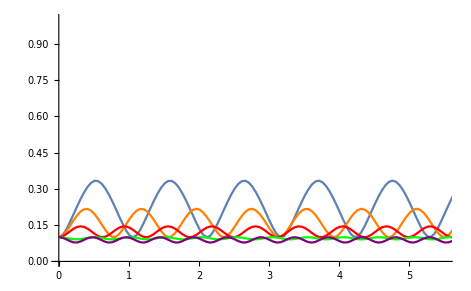

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,2,0.75μextreme[1.2247,2]],0.1,1.2247,2,0.75μextreme[1.2247,2]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,5,0.75μextreme[1.2247,5]],0.1,1.2247,5,0.75μextreme[1.2247,5]]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,10,0.75μextreme[1.2247,10]],0.1,1.2247,10,0.75μextreme[1.2247,10]]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,20,0.75μextreme[1.2247,20]],0.1,1.2247,20,0.75μextreme[1.2247,20]]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,25,0.75μextreme[1.2247,25]],0.1,1.2247,25,0.75μextreme[1.2247,25]]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

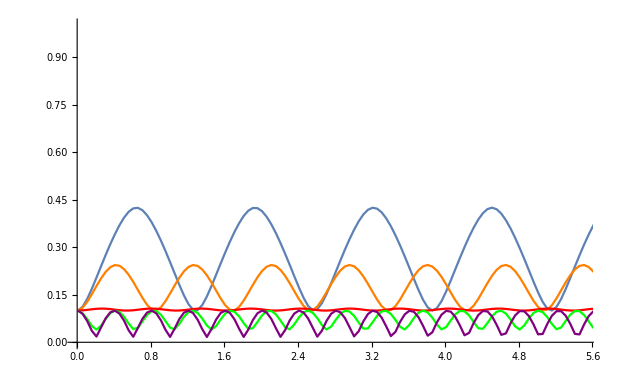

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
Show[
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,1,0.75μextreme[1.2247,1]],0.1,1.2247,1,0.75μextreme[1.2247,1]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,4,0.75μextreme[1.2247,4]],0.1,1.2247,4,0.75μextreme[1.2247,4]]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,16,0.75μextreme[1.2247,16]],0.1,1.2247,16,0.75μextreme[1.2247,16]]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,64,0.75μextreme[1.2247,64]],0.1,1.2247,64,0.75μextreme[1.2247,64]]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Abs[fz1[i,1.5qcrit[0.1,1.2247,256,0.75μextreme[1.2247,256]],0.1,1.2247,256,0.75μextreme[1.2247,256]]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},{0,1}},AxesOrigin->{0,0}
]
]
```

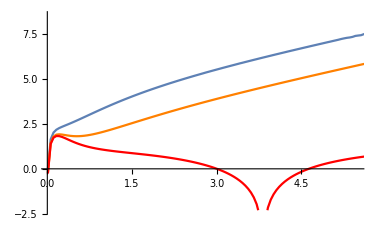

```mathematica
Block[
{qcrit,zm1,fz1,dfz1,pz,m,q,f,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Abs[pz[i,0,0.1,1,2,0.75μextreme[1,2]]]//Log},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Abs[pz[i,0.8qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]//Log},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Abs[pz[i,qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]//Log},{i,0.01,7,0.05}],PlotStyle->Red],PlotRange->{{0.01,5.5},All},AxesOrigin->{0,0}
]
]
```

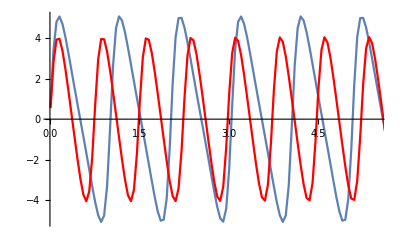

```mathematica
Block[
{qcrit,zm1,fz1,dfz1,pz,m,q,f,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Re[pz[i,2.0qcrit[0.1,1,2,0.75μextreme[1,2]],0.1,1,2,0.75μextreme[1,2]]]},{i,0.01,7,0.05}],PlotStyle->Red],PlotRange->{{0.01,5.5},All},AxesOrigin->{0,0}
]
]
```

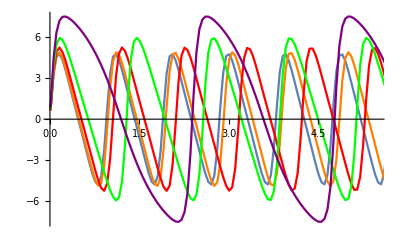

```mathematica
Block[
{qcrit,zm1,fz1,dfz1,pz,m,q,f,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,0.01,2,0.75μextreme[0.01,2]],0.1,0.01,2,0.75μextreme[0.01,2]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,0.6124,2,0.75μextreme[0.6124,2]],0.1,0.6124,2,0.75μextreme[0.6124,2]]]},{i,0.01,7,0.05}],PlotStyle->Orange],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,2,0.75μextreme[1.2247,2]],0.1,1.2247,2,0.75μextreme[1.2247,2]]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.8371,2,0.75μextreme[1.8371,2]],0.1,1.8371,2,0.75μextreme[1.8371,2]]]},{i,0.01,7,0.05}],PlotStyle->Green],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,2.4250,2,0.75μextreme[2.4250,2]],0.1,2.4250,2,0.75μextreme[2.4250,2]]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},All},AxesOrigin->{0,0}
]
]
```

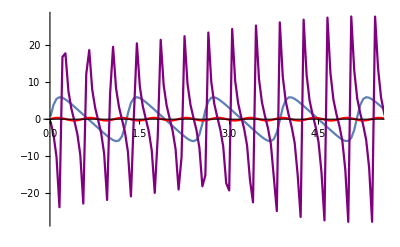

```mathematica
Block[
{qcrit,zm1,fz1,m,q,f,μextreme,dfz1,pz},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
zm1[q1_,zs1_,β1_,γ1_,μ1_]:=NDSolveValue[
{-(q μ)/(√(1+γ μ^2 z[t]^4))+(18 √6 γ (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/((1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))^2 √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2)/(z[t]^2 (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+1/(√6 z[t]^2)(√(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2)/(√6 z[t] √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))-(6 √6 γ z''[t])/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) √(6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))+(6 √6 γ z'[t]^2 (-3 β^2 z[t]+(3 (-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^2)/(2 γ)+4 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^3-(μ^2 z[t]^3)/(√(1+γ μ^2 z[t]^4))+μ^2 z[t]^3 (-Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4]+1/(√(1+γ μ^2 z[t]^4)))+(54 γ z[t] (-2 β^2 γ+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^2) z'[t]^2)/(-1-6 γ+3 β^2 γ z[t]^2+(1+6 γ-3 β^2 γ-√(1+γ μ^2)+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+√(1+γ μ^2 z[t]^4))^2-(36 γ z''[t])/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4))))/(z[t] (1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)) (6-3 β^2 z[t]^2+((-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3)/γ+2 μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4+(1-√(1+γ μ^2 z[t]^4))/γ-(36 γ z'[t]^2)/(1+6 γ-3 β^2 γ z[t]^2+(-1+3 (-2+β^2) γ+√(1+γ μ^2)-2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]) z[t]^3+2 γ μ^2 Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 z[t]^4] z[t]^4-√(1+γ μ^2 z[t]^4)))^(3/2))==0/.{q->q1,β->β1,γ->γ1,μ->μ1},z[0]== zs1,z'[0]==0},z,{t,0.01,7}
];
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
fz1[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=zm1[q1,zs1,β1,γ1,μ1][t1];
dfz1[t_,q1_,zs1_,β1_,γ1_,μ1_]:=D[fz1[t1,q1,zs1,β1,γ1,μ1],t1]/.{t1->t};
pz[t1_,q1_,zs1_,β1_,γ1_,μ1_]:=Block[
{zd,z2,fz},
z2=fz1[t1,q1,zs1,β1,γ1,μ1];
fz=f[z2,β1,γ1,μ1];
zd=dfz1[t1,q1,zs1,β1,γ1,μ1];
Return[1/z2/fz zd/Sqrt[fz-zd^2/fz]];
];
Show[
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,1,0.75μextreme[1.2247,1]],0.1,1.2247,1,0.75μextreme[1.2247,1]]]},{i,0.01,7,0.05}]],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,16,0.75μextreme[1.2247,16]],0.1,1.2247,16,0.75μextreme[1.2247,16]]]},{i,0.01,7,0.05}],PlotStyle->Red],
ListLinePlot[Table[{i,Re[pz[i,1.5qcrit[0.1,1.2247,256,0.75μextreme[1.2247,256]],0.1,1.2247,256,0.75μextreme[1.2247,256]]]},{i,0.01,7,0.05}],PlotStyle->Purple],
PlotRange->{{0.01,5.5},All},AxesOrigin->{0,0}
]
]
```